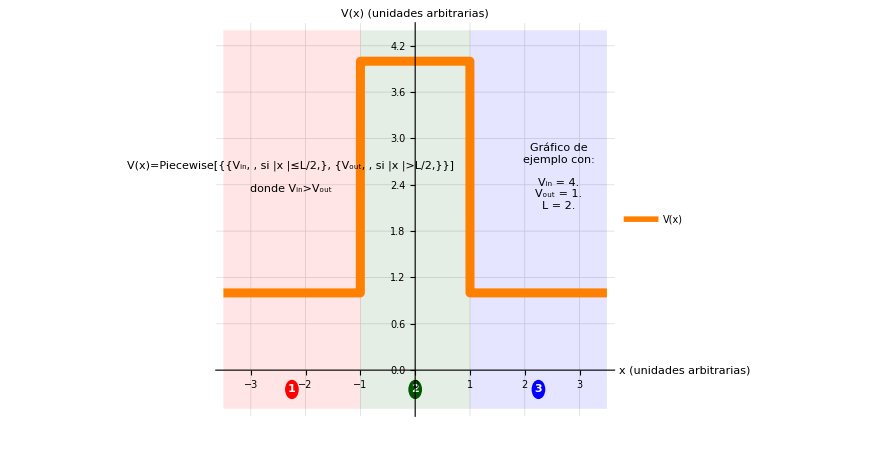

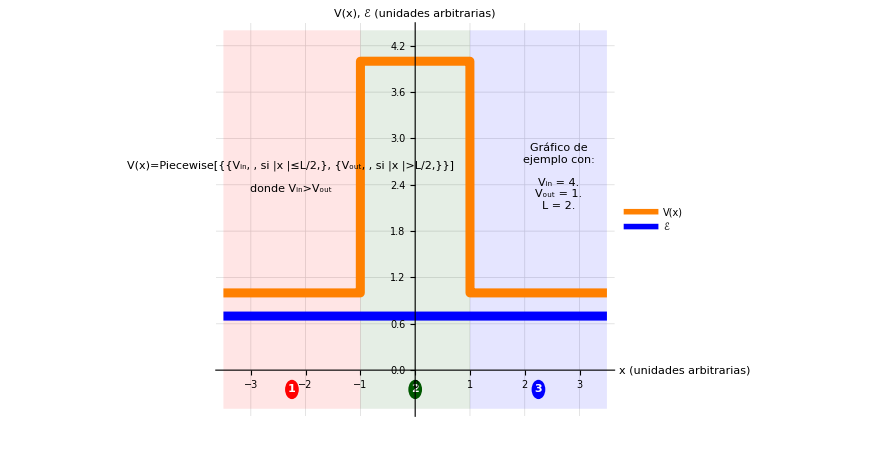

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->14}];
xmax=3.5;
ymin=-0.5;
Subscript[V, in]=4.0;
Subscript[V, out]=1.0;
L=2.0;
ℰ=0.7;

Subscript[V, min]=Min[{Subscript[V, in],Subscript[V, out]}];
Subscript[V, max]=Max[{Subscript[V, in],Subscript[V, out]}];
ymax=Piecewise[{{2ℰ-Subscript[V, max], ℰ≥Subscript[V, max]}, {1.1 Subscript[V, max], Subscript[V, max]≥ℰ}}];


txt1=Graphics[Text["V(x)=Piecewise[{{V_in, , si |x |≤L/2,}, {V_out, , si |x |>L/2,}}]\n\ndonde V_in>V_out",
				{-0.65xmax,2.5},
				BaseStyle->{TraditionalForm,Larger}]];
txt2=Graphics[Text["Gráfico de\nejemplo con:\n\nV_in = "<>ToString[Subscript[V, in]]<>"\nV_out = "<>ToString[Subscript[V, out]]<>"\nL = "<>ToString[L],
				{0.75xmax,2.5},
				BaseStyle->{TraditionalForm,Larger}]];

opc=0.1;
colors={Red,DarkGreen,Blue};
reglims=({{-xmax, -L/2, +L/2}, {-L/2, +L/2, xmax}});

regions=Table[{Directive[colors[[j]],Opacity[opc]],
			EdgeForm[None],
			Rectangle[{reglims[[1,j]],ymin},{reglims[[2,j]],ymax}]},
			{j,1,3}];

rnum=0.5Abs[ymin/2];
txtrs=Table[Graphics[{
					{colors⟦j⟧,Disk[#,rnum]},
					Text[Style[j,Bold,White],#]
				},ImageSize->24]&
				[{(reglims⟦1,j⟧+reglims⟦2,j⟧)/2,0.5ymin}],
			{j,1,3}];

colores={Orange,Blue};

	(* ********************************************** *)

	plot1=Plot[Subscript[V, out]+(Subscript[V, in]-Subscript[V, out])Boole[Abs[x]<1],
			{x,-xmax,xmax},
			Exclusions->None,
			PlotRange->{{-xmax,xmax},{ymin,ymax}},
			GridLines->Automatic,
			PlotStyle->(Directive[#,Thickness[0.01]]&/@{colores[[1,All]]}),
			AxesLabel->{"x\n(unidades\narbitrarias)","V(x) (unidades arbitrarias)"}
			];
	leyenda1=LineLegend[Directive[#,AbsoluteThickness[4]]&/@colores,
					{TraditionalForm[V[x]]},
					LabelStyle->{FontFamily->"Times",FontSize->14}];
	Final1=
		Show[plot1,txt1,txt2,txtrs,
			Prolog->regions,
			ImageSize->650,
			AspectRatio->Automatic,
			PlotRangeClipping->False,
			ImagePadding->{{2,115},{15,30}},
			Epilog->Inset[leyenda1,
						{1.03 xmax,Subscript[V, min]+(Subscript[V, max]-Subscript[V, min])/2},
						{Left,Center}]
			]
	Nombre1=NotebookDirectory[]<>"Barrera_G01_Fig";
	Export[Nombre1<>".svg",Final1];

	(* ********************************************** *)

	plot2=Plot[{Subscript[V, out]+(Subscript[V, in]-Subscript[V, out])Boole[Abs[x]<1],(ℰ+0x)},
			{x,-xmax,xmax},
			Exclusions->None,
			PlotRange->{{-xmax,xmax},{ymin,ymax}},
			GridLines->Automatic,
			PlotStyle->(Directive[#,Thickness[0.01]]&/@colores),
			AxesLabel->{"x\n(unidades\narbitrarias)","V(x), ℰ (unidades arbitrarias)"}
			];
	leyenda2=LineLegend[Directive[#,AbsoluteThickness[4]]&/@colores,
					{TraditionalForm[V[x]],TraditionalForm["ℰ"]},
					LegendLayout->If[ℰ<Subscript[V, out],"Column","ReversedColumn"],
					LabelStyle->{FontFamily->"Times",FontSize->14}];
	Final2=
		Show[plot2,txt1,txt2,txtrs,
			Prolog->regions,
			ImageSize->650,
			AspectRatio->Automatic,
			PlotRangeClipping->False,
			ImagePadding->{{2,115},{15,30}},
			Epilog->Inset[leyenda2,
						{1.03 xmax,If[ℰ<Subscript[V, out], ℰ+(Subscript[V, out]-ℰ)/2, Subscript[V, out]+(ℰ-Subscript[V, out])/2]},
						{Left,Center}]
			]
	Nombre2=NotebookDirectory[]<>Piecewise[{{"Barrera_A01_Fig", ℰ>Subscript[V, max]}, {"Barrera_B01_Fig", Subscript[V, max]≥ℰ>Subscript[V, min]}, {"Barrera_C01_Fig", Subscript[V, min]≥ℰ}}];
	Export[Nombre2<>".svg",Final2];
```